# functions

```mathematica
TimestampToDateObject[timestamp_]:=Module[
{format},(*Determine the appropriate format based on the length of the timestamp*)
format=If[
StringLength[timestamp]==19,
{"Year","-","Month","-","Day","-","Hour","-","Minute","-","Second"},
{"Year","-","Month","-","Day","-","Hour","-","Minute"}
];
(*Create the DateObject using the determined format*)
DateObject[{timestamp,format}]
]
```

```mathematica
TimeSinceMidnight[dateObj_DateObject]:=
Module[
{dateList,timePassed},

(*Extract the date list from the DateObject*)
dateList=DateList[dateObj];
(*Check if the date list contains hour,minute,and second information*)
If[
Length[dateList]>=6,
(*Calculate time passed since midnight in seconds*)
timePassed=3600dateList[[4]]+60dateList[[5]]+dateList[[6]];
timePassed,
(*Return-1 if granularity is insufficient*)
-1
]
]
```

# load & set

## set

```mathematica
dataRoot=StringRiffle[Join[Drop[StringSplit[NotebookDirectory[],"\\"],-1],{"data"}],"\\"];
```

```mathematica
configRoot=StringRiffle[Join[Drop[StringSplit[NotebookDirectory[],"\\"],-1],{"system_config"}],"\\"];
```

## load

```mathematica
roomsConfig=Module[
{configRaw},
configRaw=Import[configRoot<>"\\rooms.json","JSON"];
Table[
{room,"name","sensor"}/.(ToString[room]/.configRaw)
,{room,1,Length[configRaw]}]
];
roomNum=Length[roomsConfig];
```

```mathematica
roomsTempAndHumidity=Module[
{roomLogs,roomsTempAndHumidityRaw},
roomLogs=Map[Import[#,"Text"]&,FileNames[All,dataRoot<>"\\logs\\temperature_and_humidity"]];
roomsTempAndHumidityRaw=Table[
Map[ImportString[#,"JSON"]&,StringSplit[roomLog,"\n"]]
,{roomLog,roomLogs}];
Table[
ToString[room]/.Flatten[roomsTempAndHumidityRaw,1]
,{room,1,roomNum}]
];
```

```mathematica
summerWeather=Import[dataRoot<>"\\external\\weather\\temp_and_hum_2024_summer.csv","CSV"];
```

# elemzés

## nyári hőmérsékletek

```mathematica
roomsConfig[[roomsWithData]][[All,2]]
```

{ovi,PK,SZGK,Mérce,Gólyairoda,kisterem,vendégtér}

```mathematica
roomsConfig[[All,2]]
```

{Oktopusz,ovi,PK,SZGK,Mérce,Lahmacun,Gólyairoda,kisterem,vendégtér}

```mathematica
roomCoolingMethods={"no data","belső függöny","belső függöny","külső árnyékolás","belső függöny + mobilklíma","no data","nem utcai oldal","belső függöny","belső függöny"};
```

```mathematica
roomCoolingMethods[[roomsWithData]]
```

{belső függöny,belső függöny,külső árnyékolás,belső függöny + mobilklíma,nem utcai oldal,belső függöny,belső függöny}

```mathematica
roomsWithData=Transpose[Select[roomsConfig,#[[3]]!="none"&]][[1]];
```

```mathematica
roomTemps=Table[
{
roomsConfig[[room]][[2]],
Map[
{
TimestampToDateObject[#[[1]]],
N[#[[2]]/100]
}&
,SortBy[{"last_updated","temp"}/.roomsTempAndHumidity[[room]],First]
]
},{room,roomsWithData}];
```

```mathematica
externalTemp=Map[
{
TimestampToDateObject[#[[1]]],
#[[2]]
}
&,Drop[summerWeather,1][[All,{1,2}]]];
```

```mathematica
externalHum=Map[
{
TimestampToDateObject[#[[1]]],
#[[2]]
}
&,Drop[summerWeather,1][[All,{1,3}]]];
```

```mathematica
externalWind=Map[
{
TimestampToDateObject[#[[1]]],
#[[2]]
}
&,Drop[summerWeather,1][[All,{1,4}]]];
```

```mathematica
weatherCondition=Map[
{
TimestampToDateObject[#[[1]]],
#[[2]]
}
&,Drop[summerWeather,1][[All,{1,5}]]];
```

```mathematica
roomCols=Table[RGBColor[n/8,1-n/8,0.5],{n,1,Length[roomsWithData]}];
```

```mathematica
roomNames=roomsConfig[[roomsWithData]][[All,2]];
```

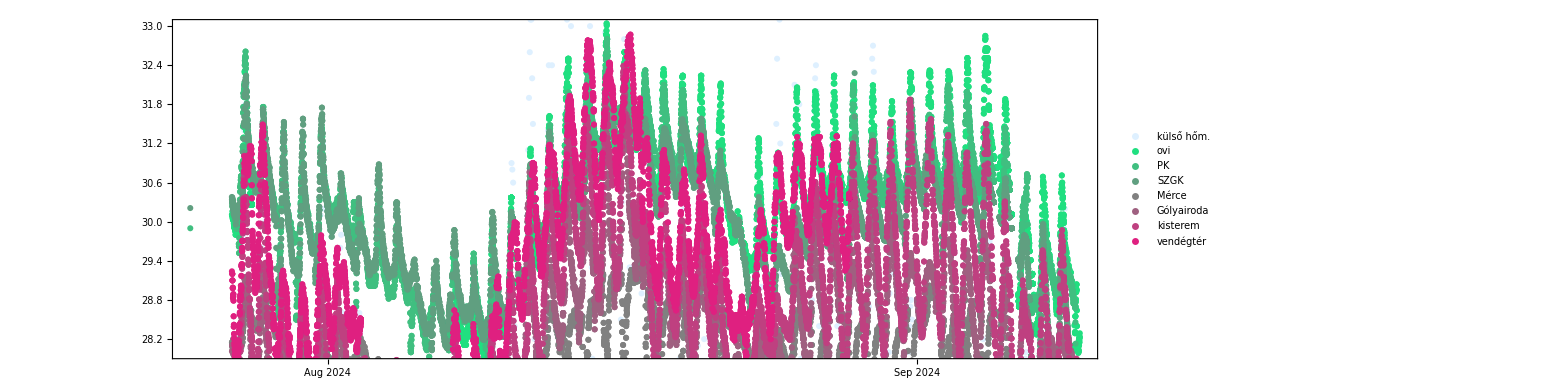

```mathematica
DateListPlot[
Join[
{externalTemp},
Map[#[[2]]&,roomTemps]
],Joined->False,PlotStyle->Join[{LightBlue},roomCols],
AspectRatio->0.25,ImageSize->2000,PlotLegends->Join[{"külső hőm."},roomsConfig[[roomsWithData]][[All,2]]],PlotRange->{All,{28,33}}
]
```

```mathematica
roomsTempWithRelativeTimestamp=Table[Map[
{
roomTemps[[roomN]][[1]],
#[[1]],
DateDifference[DateObject[{2024,7,27,0,0,0}],#[[1]],"Day"][[1]],
DateDifference[DateObject[{2024,7,27,0,0,0}],#[[1]],"Hour"][[1]],
TimeSinceMidnight[#[[1]]],
#[[2]]
}&,
roomTemps[[roomN]][[2]]
],{roomN,1,Length[roomsWithData]}];
```

```mathematica
externalTempWithRelativeTimestamp=Map[
{
0,
#[[1]],
DateDifference[DateObject[{2024,7,27,0,0,0}],#[[1]],"Day"][[1]],
DateDifference[DateObject[{2024,7,27,0,0,0}],#[[1]],"Hour"][[1]],
TimeSinceMidnight[#[[1]]],
#[[2]]
}&,
externalTemp
];
```

```mathematica
hourlyUnifiedData=GatherBy[Flatten[Join[{externalTempWithRelativeTimestamp},roomsTempWithRelativeTimestamp],1],Floor[#[[4]]]&];
```

```mathematica
referencedData=Flatten[Table[Module[
{hourlyMeans},
hourlyMeans=Table[
Join[
{hourlyData[[1]][[2]]},
Module[
{roomDataPoints},
roomDataPoints=Select[
hourlyData,
#[[1]]==room&
];
If[
Length[roomDataPoints]!=0,
Mean[roomDataPoints][[{1,3,4,5,6}]],
{room,None,None,None,None}
]
]
],{room,Join[roomsWithData,{0}]}];
Select[Flatten[Table[Table[
Module[
{room1Data,room2Data,externalData},
room1Data=hourlyMeans[[room1N]];
room2Data=hourlyMeans[[room2N]];
externalData=hourlyMeans[[-1]];
{
room1Data[[1]],(*1 timestamp*)
room1Data[[3]],(*2 eltelt napok*)
room1Data[[5]],(*3 másodperc éjfél óta aznap*)
roomsWithData[[{room1N,room2N}]],(*4 melyik szobák*)
room1Data[[6]]-externalData[[6]],(*5 kinthez viszonyított hőmérséklet*)
externalData[[6]],(*6 kinti hőmérséklet*)
room1Data[[6]],(*7 hőmérséklet*)
room1Data[[6]]-room2Data[[6]](*8 másik szobához viszonyított hőmérséklet*)
}
]
,{room2N,1,Length[roomsWithData]}],{room1N,1,Length[roomsWithData]}],1],NumberQ[Total[#[[{2,3,5,6,7}]]]]&&#[[4]][[1]]!=#[[4]][[2]]&]
],{hourlyData,hourlyUnifiedData}],1];
```

```mathematica
referencedDataColumns={"1 timestamp","2 eltelt napok","3 másodperc éjfél óta aznap","4 melyik szobák","5 kinthez viszonyított hőmérséklet","6 kinti hőmérséklet","7 hőmérséklet","8 másik szobához viszonyított hőmérséklet"};
```

```mathematica
Export[NotebookDirectory[]<>"data\\summer_temps\\referencedData.mx",referencedData];
```

```mathematica
referencedData=Import[NotebookDirectory[]<>"data\\summer_temps\\referencedData.mx"];
```

```mathematica
roomData=Select[
referencedData,
#[[4]][[1]]==room&&#[[4]][[1]]!=#[[4]][[2]]&
];
```

```mathematica
roomsDailyTempProfile=Table[Table[
Module[
{hourlyData},
hourlyData=Select[
Select[
referencedData,
#[[4]][[1]]==room&&#[[4]][[1]]!=#[[4]][[2]]&
],
Between[#[[3]],{hour 3600,(hour+1) 3600}]&
];
Flatten[{
Mean[hourlyData[[All,3]]]/3600,
GetMeanAndSD[hourlyData[[All,7]]]
}]
]
,{hour,0,23}],{room,roomsWithData}];
```

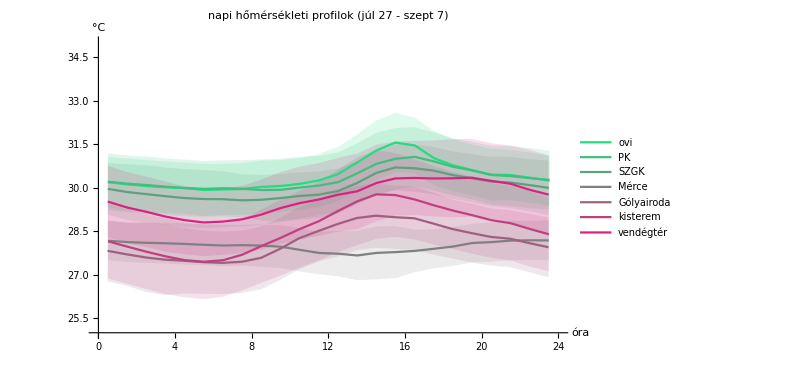

```mathematica
dailyTempProfilesPlot=ErrorListPlot[
Map[Transpose,roomsDailyTempProfile],
roomCols,
{
PlotRange->{{0,24},{25,35}},
AxesOrigin->{0,25},PlotLegends->Placed[roomNames,Below],ImageSize->600,
PlotLabel->"napi hőmérsékleti profilok (júl 27 - szept 7)",
AxesLabel->{"óra","°C"}
},
{True,True,False}
]
```

```mathematica
Export[NotebookDirectory[]<>"plots\\summer_temps\\napi hőmérsékleti profilok.png",dailyTempProfilesPlot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazanfutes\analysis\plots\summer_temps\napi hőmérsékleti profilok.png

```mathematica
roomsDailyTempDiffToExternalTempProfile=Table[Table[
Module[
{hourlyData},
hourlyData=Select[
Select[
referencedData,
#[[4]][[1]]==room&&#[[4]][[1]]!=#[[4]][[2]]&&
30<#[[6]]&
],
Between[#[[3]],{hour 3600,(hour+1) 3600}]&
];
Flatten[{
Mean[hourlyData[[All,3]]]/3600,
GetMeanAndSD[hourlyData[[All,5]]]
}]
]
,{hour,12,20}],{room,roomsWithData}];
```

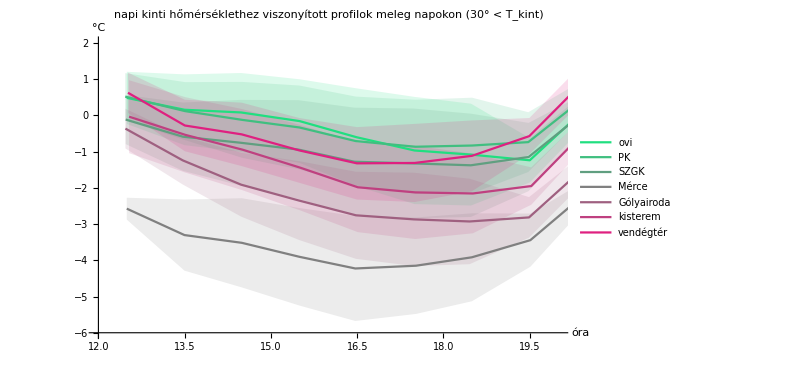

```mathematica
roomsDailyTempDiffToExternalTempProfilePlot=ErrorListPlot[
Map[Transpose,roomsDailyTempDiffToExternalTempProfile],
roomCols,
{
PlotRange->{{12,20},{-6,2}},
AxesOrigin->{12,-6},PlotLegends->Placed[roomNames,Below],ImageSize->600,
PlotLabel->"napi kinti hőmérséklethez viszonyított profilok meleg napokon (30° < T_kint)",
AxesLabel->{"óra","°C"}
},
{True,True,False}
]
```

```mathematica
Export[NotebookDirectory[]<>"plots\\summer_temps\\meleg napi hőmérsékleti profilok kinthez képest.png",roomsDailyTempDiffToExternalTempProfilePlot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazanfutes\analysis\plots\summer_temps\meleg napi hőmérsékleti profilok kinthez képest.png

```mathematica
szgkModificationRelativeDays=DateDifference[DateObject[{2024,7,27,0,0,0}],DateObject[{2024,8,13,0,0,0}],"Day"][[1]];
```

```mathematica
room=4;
szgkModificationEffect=Table[
Select[Table[
Module[
{hourlyData},
hourlyData=Select[
Select[
referencedData,
#[[4]][[1]]==room&&#[[4]][[1]]!=#[[4]][[2]]&&
If[
before,
szgkModificationRelativeDays<=#[[2]],
szgkModificationRelativeDays>#[[2]]
]
&&
30<#[[6]]&
],
Between[#[[3]],{hour 3600,(hour+1) 3600}]&
];
Flatten[{
Mean[hourlyData[[All,3]]]/3600,
GetCentralTendencyAndWidth[hourlyData[[All,5]],Mean,StandardDeviation]
}]
]
,{hour,0,23}],NumberQ[Total[#]]&]
,{before,{True,False}}];
```

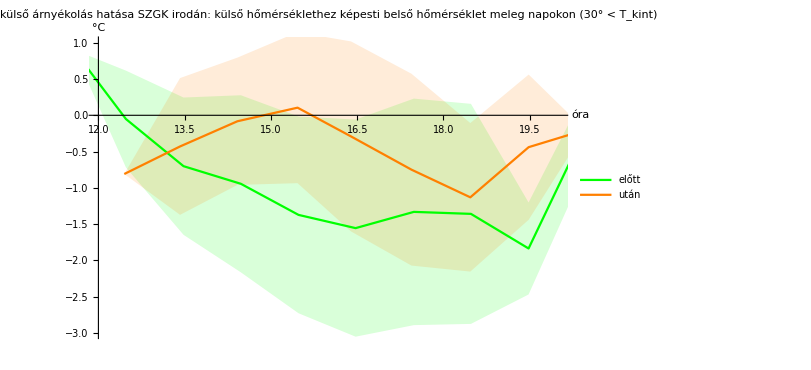

```mathematica
szgkModificationEffectPlot=ErrorListPlot[
Map[Transpose,szgkModificationEffect],
{Green,Orange},
{
PlotRange->{{12,20},{-3,1}},
AxesOrigin->{12,0},PlotLegends->{"előtt","után"},ImageSize->600,
PlotLabel->"külső árnyékolás hatása SZGK irodán:\nkülső hőmérséklethez képesti belső hőmérséklet meleg napokon (30° < T_kint)",
AxesLabel->{"óra","°C"}
},
{True,True,False}
]
```

```mathematica
Export[NotebookDirectory[]<>"plots\\summer_temps\\SZGK árnyékolás hatása.png",szgkModificationEffectPlot]
```

C:\Users\Beno\Documents\SZAKI\dev\kazanfutes\analysis\plots\summer_temps\SZGK árnyékolás hatása.png